```mathematica
$Path=Prepend[$Path,"E:\\HOME\\anton\\roundabout"];
```

```mathematica
<<"ACPackages`"
<<"ErrorBarPlots`"
```

ErrorListPlot::shdw: Symbol ErrorListPlot appears in multiple contexts ErrorBarPlots`Graphics`Graphics`; definitions in context ErrorBarPlots` may shadow or be shadowed by other definitions.

```mathematica
$WD=SetWorkDir[];
```

```mathematica
$WD=NotebookDirectory[];
```

```mathematica
SetWorkDir["/2006.07.20/Re=10"];
```

```mathematica
(*Table of results: list of {date(year,month,day),mesh(Nx=Nz),Re,r/R,gamma,F(r),Coriolis;shift,mvx,δmvx,mvy,δmvy,mvz,δmvz,Evx,δEvx,Evy,δEvy,Evz,δEvz,mψ,δmψ,comment}*)
indepkol=9;
depkol=15;
```

## Добавление записей

```mathematica
dvx=dvy=dvz=0;
dqvx=dqvy=dqvz=0;
```

```mathematica
{dvx,dvy,dvz,dqvx,dqvy,dqvz}={6 10^-6,1 10^-8,6 10^-7,3 10^-9,5 10^-9,3 10^-9};
```

```mathematica
{dvx,dvy,dvz,dqvx,dqvy,dqvz}={0,6 10^-5,0,0,2 10^-5,0};
```

```mathematica
putlist=Join[{2010,01,14},{64},{Rm=10,kappa=0.5,gamma=10^-4,Fr="dp1",Coriolis=0,shift,maxvx,dvx,maxvy,dvy,maxvz,dvz,mqvx,dqvx,mqvy,dqvy,mqvz,dqvz,Max[Abs[ψ]],Max[Abs[ψ2-ψ1]],"ErrScale 1e-4"}]/.b_:>CForm[b]/;NumericQ[b]
```

{2010,1,14,64,10,0.5,0.0001,dp1,0,-0.15484593957308104,0.06795745809105394,6.e-6,0.9790211100154612,1.e-8,0.043017128575658856,6.e-7,0.0006104661380527778,3.e-9,0.24495154816498063,5.e-9,0.00021323193049960375,3.e-9,0.020974286874999998,0.010065316875000008,ErrScale 1e-4}

```mathematica
putlist>>>($WD<>"\\result.dat")
{Rm,kappa,gamma,Fr,Coriolis,shift,maxvx,dvx,maxvy,dvy,maxvz,dvz,mqvx,dqvx,mqvy,dqvy,mqvz,dqvz,ψ,ψ2,ψ1}=.;
```

## Анализ записей

### Функции

```mathematica
UpdateData:=Block[{},Print[fields=Module[{res,stm},res=ReadList[stm=StringToStream[First[ReadList[$WD<>"\\result.dat"]]],Word,WordSeparators->{" ",",","{","}"}];Close[stm];res]];
all=Select[Rest[ReadList[$WD<>"\\result.dat"]]/.{a_+b_ E->b*10^a}/.{a_+b_ e->b*10^a},StringFreeQ[Last[#],"wrong"]&];
Print["Total:",Length[all]," records"];]
```

```mathematica
MakeRule[el_]:=MapThread[Rule,{fields,el}];
```

```mathematica
ShowDependance[param_,funcs_,conditions_:{}]:=Block[{allbut=GetResults[conditions],dep,deplist,numpar,othern,otherv},If[FreeQ[Drop[fields,{indepkol+1,-2}],param],Print["Wrong parameter"];Return[]];numpar=First[Flatten[Position[fields,param]]];othern=Complement[Join[Range[4,Length[fields]-depkol-1],{Length[fields]}],{numpar}];Print["All such parameters=",Union[(#1⟦numpar⟧&)/@allbut]];dep=First[Rest[Reap[(Sow[#1,NotList@@#1⟦othern⟧]&)/@Sort[allbut,N[#1⟦numpar⟧]<N[#2⟦numpar⟧]&],_,f]]];dep=Select[dep,Length[Last[#1]]>1&];
(*Print["dep=",dep];*)
otherv=Drop[Drop[Drop[fields,{indepkol+1,-2}],{numpar}],3];Print[otherv];nom=0;If[Length[dep]==0,Print["Data was not found"];Return[]];Print["Plots can be shown for parameters:"];(Print["№",++nom,":",MapThread[Rule,{otherv,List@@First[#1]}],", number of points=",Length[Last[#1]]]&)/@dep;If[Length[dep]>1,nom=Input["Введите номер желаемой зависимости"],nom=1];Print["So constant parameters are:"];Print["\t",Thread[otherv->List@@First[dep⟦nom⟧]]];deplist=({#1,"δ"<>#1," "<>#1}&)/@Flatten[{funcs}];pts=Join[{param},RotateRight/@deplist,{"comment"}]/.MakeRule/@Last[dep⟦nom⟧];pts=Function[l,{({{#1⟦1⟧,#1⟦2⟧},ErrorBar[#1⟦3⟧]}&)/@Flatten/@Transpose[Join[{First/@pts},{l}]],l⟦1,-1⟧}]/@Transpose[deplist/.MakeRule/@Last[dep⟦nom⟧]];
pts=Join[{param},deplist,{"comment"}]/.MakeRule/@Last[dep⟦nom⟧];(*If[param≠Last[fields],(ListPlot[{First[#1]},AxesLabel->{param,Last[#1]},Axes->True,Frame->False,PlotLabel->Last[#1],PlotMarkers->{■}]&)/@pts];*)
If[param≠Last[fields],ErrorListPlot[MapThread[{{#1,#2},ErrorBar[#3]}&,{First/@pts,#⟦All,1⟧,#⟦All,2⟧}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")",PlotRange->All]&/@Transpose[pts[[All,2;;-2]]]
]
];
```

```mathematica
GetResults[conditions_:{}]:=Block[{pattern,rules=Union[Select[conditions,Head[#]==Rule&]],
(*Unequal doesn't work always*)
ineqs=And@@Flatten[Select[conditions,MemberQ[{Less,LessEqual,Greater,GreaterEqual,Unequal},Head[#]]∨#==False&]]},
MatchesQ[el_]:=Module[{mr=MakeRule[el]},Simplify[ineqs/.mr]∧Complement[rules,mr]=={}];
Print["All data matches (",Simplify[ineqs],")",Sequence@@("&&("<>First[#]<>"="<>ToString[InputForm[Last[#]]]<>")"&/@rules),":"];
Return[Select[all,MatchesQ]];
];
```

### Действия

```mathematica
UpdateData
```

{year,month,day,Nxz,Re,r/R,gamma,F(r),Coriolis,shift,mvx,δmvx,mvy,δmvy,mvz,δmvz,Evx,δEvx,Evy,δEvy,Evz,δEvz,mψ,δmψ,comment}

Total:145 records

```mathematica
$res=GetResults[{"r/R"->0.5,"Re"->10}]
```

All data matches (True)&&(Re=10)&&(r/R=0.5):

{{2009,1,29,128,10,0.5,0.0001,dp,0,-0.154853,0.067934,8.×10^-6,0.978887,0.00004,0.0428981,0.00001,0.000606696,2.×10^-7,0.244603,0.00002,0.000212102,5.×10^-8,0.0209875,0.00940433,ErrScale 1e-4},{2009,11,13,128,10,0.5,0.0001,dp,0,-0.154111,0.0682553,0.0005,0.973814,0.001,0.0430585,0.0008,0.000613116,5.×10^-6,0.243318,0.0003,0.000214281,2.×10^-6,0.0210456,0.00944724,ErrScale 1e-4},{2009,12,4,100,10,0.5,0.0001,epsr,0,0.114994,0.0603549,0.0002,0.954567,0.0012,0.0350222,0.0001,0.000514271,4.×10^-6,0.247023,0.0005,0.00017964,1.×10^-6,0.0191209,0.00867019,ErrScale 1e-4},{2010,1,14,64,10,0.5,0.0001,dp1,0,-0.154846,0.0679575,6.×10^-6,0.979021,1.×10^-8,0.0430171,6.×10^-7,0.000610466,3.×10^-9,0.244952,5.×10^-9,0.000213232,3.×10^-9,0.0209743,0.0100653,ErrScale 1e-4}}

```mathematica
$res=GetResults[{}];
```

All data matches (True):

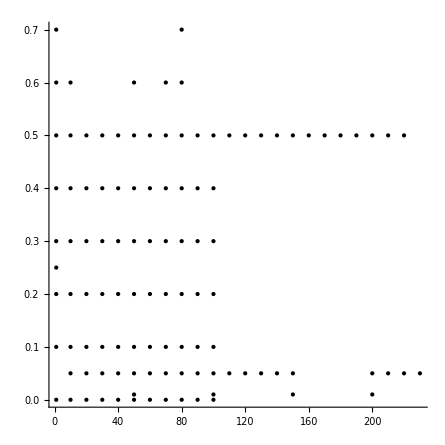

```mathematica
Graphics[Point/@Union[GetFields[#,{"Re","r/R"}]&/@$res],AspectRatio->1,Axes->True]
```

```mathematica
GetResults[{"Nxz"->128,"Ny"->5,"r/R"->1/4,"lfi"->1.,"F(r)"->1,"Coriolis"->0,"comment"->"ErrScale 1e-4"}]
```

```mathematica
ShowTable[$res,{"Nxz","Re","r/R","shift","mvx","mvy","mvz","Evx","Evy","Evz","mψ","F(r)"}]
```

Nxz | Re | r/R | shift | mvx | mvy | mvz | Evx | Evy | Evz | mψ | F(r)
128 | 10 | 0.5 | -0.154853 | 0.067934 | 0.978887 | 0.0428981 | 0.000606696 | 0.244603 | 0.000212102 | 0.0209875 | dp
128 | 10 | 0.5 | -0.154111 | 0.0682553 | 0.973814 | 0.0430585 | 0.000613116 | 0.243318 | 0.000214281 | 0.0210456 | dp
100 | 10 | 0.5 | 0.114994 | 0.0603549 | 0.954567 | 0.0350222 | 0.000514271 | 0.247023 | 0.00017964 | 0.0191209 | epsr
64 | 10 | 0.5 | -0.154846 | 0.0679575 | 0.979021 | 0.0430171 | 0.000610466 | 0.244952 | 0.000213232 | 0.0209743 | dp1

#### Все поля определённого типа

```mathematica
GetField[res_,field_String]:=Block[{num=Position[fields,field]},
If[Length[num]<1,Print["Field not found"];Return[$Failed]];
Extract[res,First[num]]
]
GetFields[res_,fs_List]:=GetField[res,#]&/@fs
ShowTable[fromres_,fs_List]:=Prepend[GetFields[#,fs]&/@fromres,fs]//TableForm
```

```mathematica
GetField[Union/@Transpose[$res],"r/R"]
```

{0,0.1,0.2,0.3,0.4,0.5}

```mathematica
MapThread[Join[{#1},#2]&,{fields,Union/@Transpose[$res]}]//TableForm
```

```mathematica
Select[MapThread[Join[{#1},#2]&,{fields,Union/@Transpose[$res]}],Length[#]>3&]//TableForm
```

### Зависимости

```mathematica
allfuncs=Select[Take[fields,{indepkol+1,-2}],Length[StringPosition[#,"δ"]]==0&]
```

{shift,mvx,mvy,mvz,Evx,Evy,Evz,mψ}

All data matches (True):

All such parameters={0,0.1,0.2,0.25,0.3,0.4,0.5,0.6,0.7}

{Nxz,Re,gamma,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Nxz→128,Re→90,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=6

№2:{Nxz→128,Re→80,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=8

№3:{Nxz→256,Re→70,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№4:{Nxz→128,Re→70,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=7

№5:{Nxz→128,Re→60,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=6

№6:{Nxz→128,Re→50,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=7

№7:{Nxz→128,Re→40,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=8

№8:{Nxz→128,Re→30,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=6

№9:{Nxz→128,Re→20,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=6

№10:{Nxz→128,Re→10,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=6

№11:{Nxz→100,Re→1,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=7

So constant parameters are:

{Nxz→128,Re→20,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}

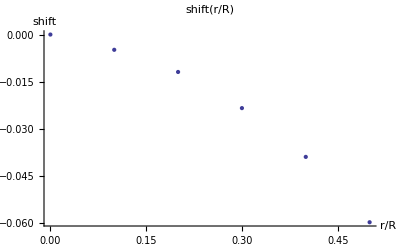
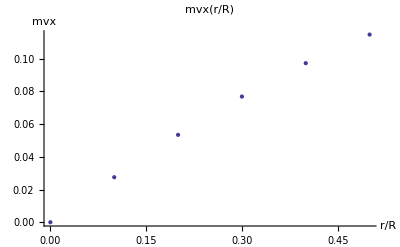
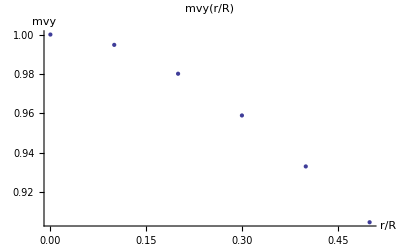
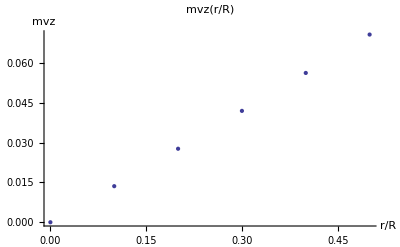
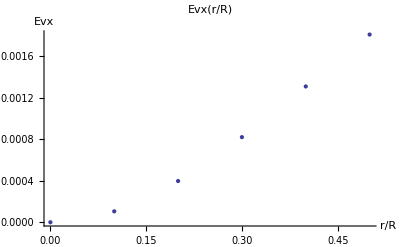
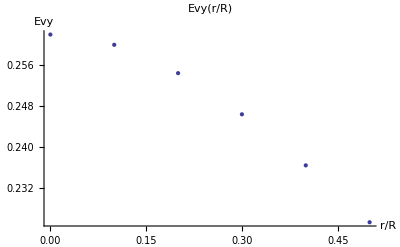
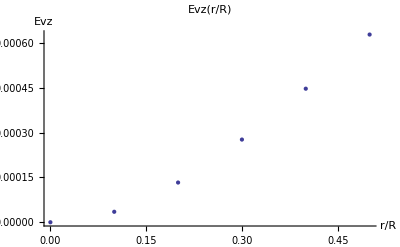
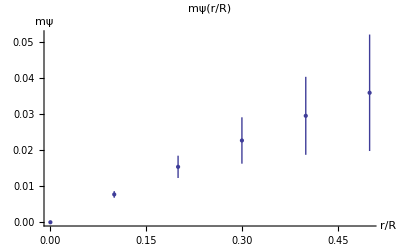

```mathematica
ShowDependance["r/R",allfuncs]
```

All data matches (True):

All such parameters={1,10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200}

{Nxz,r/R,gamma,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Nxz→128,r/R→0.05,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=17

№2:{Nxz→128,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=24

№3:{Nxz→128,r/R→0.4,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=10

№4:{Nxz→128,r/R→0.3,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=10

№5:{Nxz→128,r/R→0.2,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=11

№6:{Nxz→128,r/R→0.1,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=11

№7:{Nxz→128,r/R→0,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=10

№8:{Nxz→128,r/R→0.6,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=3

So constant parameters are:

{Nxz→128,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}

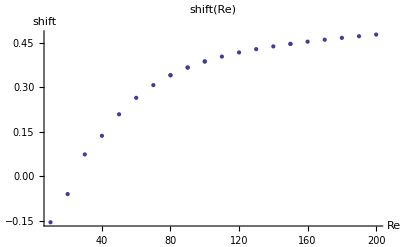
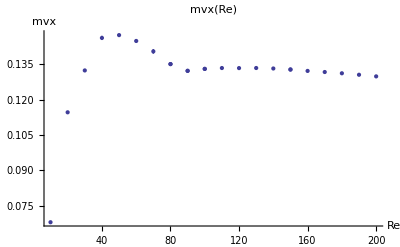
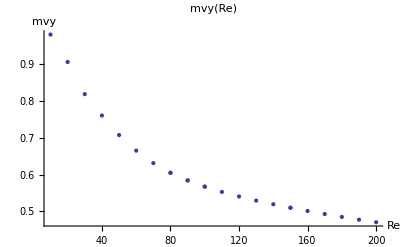
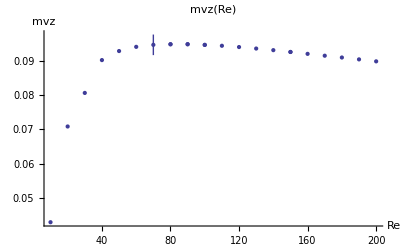
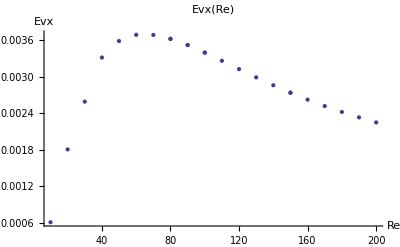
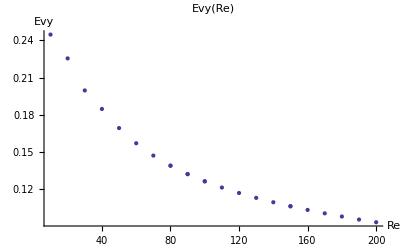
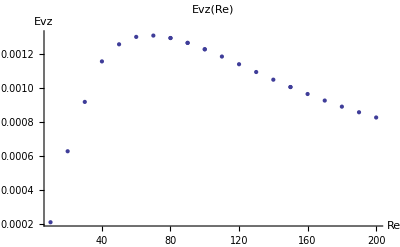
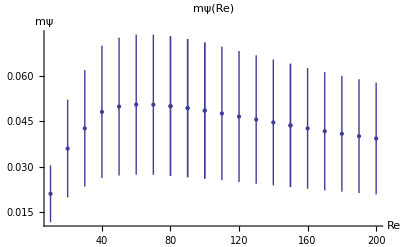

```mathematica
ShowDependance["Re",allfuncs]
```

All data matches (True):

All such parameters={10,20,30,40,50,60,70,80,90,100,110,128,256}

{Re,r/R,gamma,F(r),Coriolis,comment}

Plots can be shown for parameters:

№1:{Re→1,r/R→0.25,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=11

№2:{Re→150,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№3:{Re→100,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№4:{Re→90,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№5:{Re→80,r/R→0.5,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№6:{Re→10,r/R→0.05,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№7:{Re→70,r/R→0.1,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№8:{Re→70,r/R→0,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№9:{Re→40,r/R→0.2,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

№10:{Re→40,r/R→0.1,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}, number of points=2

So constant parameters are:

{Re→1,r/R→0.25,gamma→0.0001,F(r)→1,Coriolis→0,comment→ErrScale 1e-4}

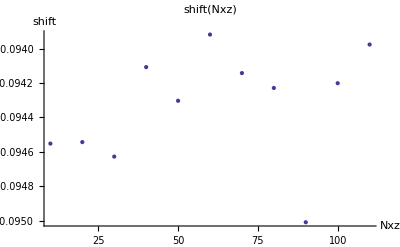
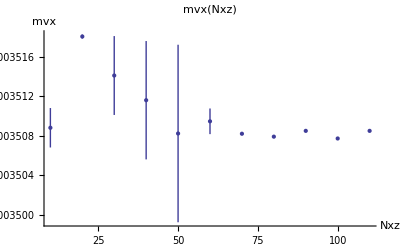
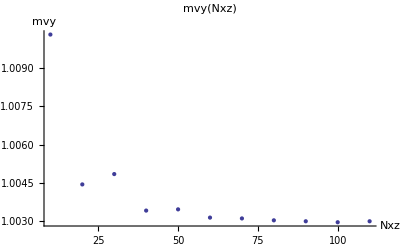
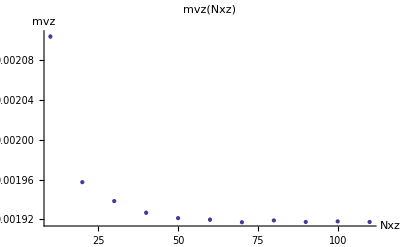
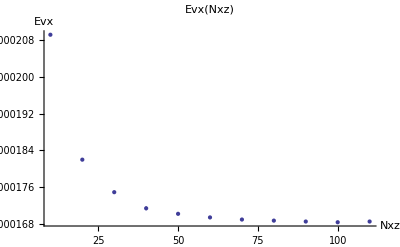
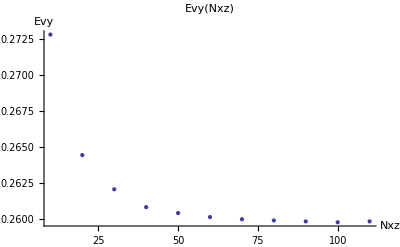
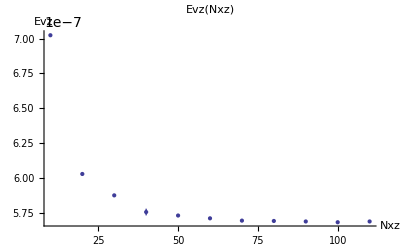
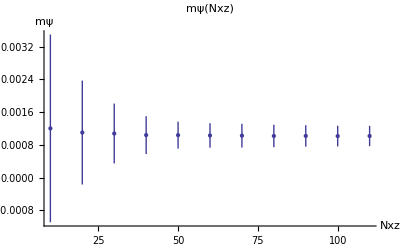

```mathematica
ShowDependance["Nxz",allfuncs]
```

```mathematica
pts//TableForm
```

```mathematica
Export[ToString[Unique[]]<>".eps",#]&/@{}
```

{$17.eps,$18.eps,$19.eps,$20.eps,$21.eps,$22.eps,$23.eps,$24.eps}

### Отдельное рисование

```mathematica
numfunc=4;
```

```mathematica
list=(Transpose[{First/@pts,{#⟦1⟧,#⟦2⟧}&/@(#[[numfunc]]&/@pts)}];
Transpose[{(1/First[#])^-1&/@pts,First[#]&/@(#[[numfunc]]&/@pts)}])
```

```mathematica
ListPlot[Drop[list,2],PlotRange->All,PlotLabel->Last[Last[(#1⟦numfunc⟧&)/@pts]],PlotStyle->PointSize[0.03]]
```

```mathematica
Transpose[pts[[All,2;;-2]]]
```

```mathematica
With[{param="lfi"},ListPlot[Transpose[{First/@pts,First/@#}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")"]&/@Transpose[pts[[All,2;;-2]]]
]
```

```mathematica
Transpose[{First/@pts,First/@pts[[All,8]]}]
```

{{0.01,3.66375},{0.1,0.00100646},{1.,0.00100646},{2 π,0.00100646}}

```mathematica
ListPlot[Rest@Transpose[{First/@pts,First/@pts[[All,8]]}]]
```

```mathematica
ListPlot[(First/@pts[[All,5]])]
```

```mathematica
With[{param="Re"},ErrorListPlot[MapThread[{{#1,#2},ErrorBar[#3]}&,{First/@pts,#⟦All,1⟧,#⟦All,2⟧}],AxesLabel->{param,#⟦-1,-1⟧},PlotLabel->#⟦-1,-1⟧<>"("<>param<>")",PlotRange->All]&/@Transpose[pts[[All,2;;-2]]]
]
```

```mathematica
Fit[Drop[list,2],{1,x},x]
```

0.990812+2.49089 x

```mathematica
PrintRange[GetFields[#,{"Re","shift"}]&/@$res]
```